```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v3

```mathematica
dataall=Table[Import["./Shi_mu=900-1200/Shi_mu="<>ToString[i]<>"_m0=700.0-51x104_VC=true.csv"],{i,880,1200,10}];
```

```mathematica
n=Length[Table[i,{i,880,1200,10}]]
```

33

```mathematica
dataall[[1]]
```

```mathematica
pdata=Table[Table[Table[dataall[[n1]][[j*104+i]][[5]],{i,2,105}],{j,0,50}],{n1,1,33}];
```

```mathematica
Table[Table[Export["./mub"<>ToString[880+(i-1)*10]<>"/V"<>ToString[j]<>".dat",pdata[[i]][[j]]],{i,1,33}],{j,1,51}];
```

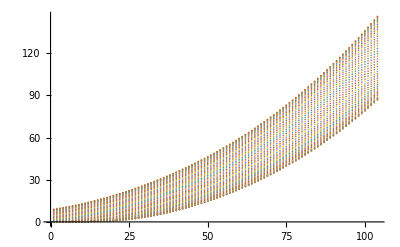

```mathematica
ListPlot[pdata[[1]]]
```